Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Sum[n^3,{n,1,6}]
nFaulhaber[3,6]
Select[nCollatz[27],OddQ]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

441

441

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes Apostol MFDSNT

1. Elliptic Functions

## 1.1 - 1.4 Elliptic functions

### Definition

A function f is called elliptic if it has the following two properties :
- f is doubly periodic;
- f is meromorphic (its only singularities in the finite plane are poles).

### Theorem 1.3

A non-constant elliptic function has a fundamental pair of periods.

### Theorem 1.4

If an elliptic function f has no poles in some period parallelogram, then f is constant.

### Theorem 1.5

If an elliptic function f has no zeros in some period parallelogram, then f is constant.

### Theorem 1.6

The contour integral of an elliptic function taken along the boundary of any cell is zero.

### Theorem 1.7

The sum of the residues of an elliptic function at its poles in any period parallelogram is zero.

### Theorem 1.8

The number of zeros of an elliptic function in any period parallelogram is equal to the number of poles, each counted with multiplicity.

## 1.5 Construction of elliptic functions

## 1.6 The Weierstrass P Function

### Weierstrass Function

```mathematica
w1=1;
w2=I;
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{w1,w2}]]
```

```mathematica
ComplexPlot3D[p[z],{z,-(2w1+2w2),(2w1+2w2)}]
```

-Graphics3D-

```mathematica
ComplexPlot[p[z],{z,0,2w1+2w2},Frame->False]
```

-Graphics-

```mathematica
ComplexPlot[p[z]^15+p[z]^10+p[z]^5+p[z],{z,-(2w1+2w2),2w1+2w2},Frame->False]
```

-Graphics-

#### Some other graphs

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

### Derivative of Weierstrass Function

```mathematica
w1=1;
w2=I;
p1[z_]:=WeierstrassPPrime[z,WeierstrassInvariants[{w1,w2}]]
```

```mathematica
ComplexPlot3D[p1[z],{z,-(2w1+2w2),(2w1+2w2)}]
```

-Graphics3D-

```mathematica
ComplexPlot[p1[z],{z,-(2w1+2w2),(2w1+2w2)}]
```

-Graphics-

#### Zeros of the derivative of the Weierstrass Function

```mathematica
WeierstrassPPrime[3,WeierstrassInvariants[{w1,w2}]]//N//Chop
WeierstrassPPrime[3I,WeierstrassInvariants[{w1,w2}]]//N//Chop
WeierstrassPPrime[2+3I,WeierstrassInvariants[{w1,w2}]]//N//Chop
```

0

0

0

## 1.7 The Laurent expansion of the Weierstrass function

### Laurent Series WeierstrassP

```mathematica
1+√-3/2//N
```

1.+0.866025 ⅈ

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,(1+√-3)/2}]],{z,0,18}]
```

1/z^2+(Gamma[1/3]^18 z^4)/(114688 π^6)+(Gamma[1/3]^36 z^10)/(170993385472 π^12)+(Gamma[1/3]^54 z^16)/(372606898467241984 π^18)+O[z]^19

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,1+I}]],{z,0,18}]
```

1/z^2+(Gamma[1/4]^8 z^2)/(5120 π^2)+(Gamma[1/4]^16 z^6)/(78643200 π^4)+(Gamma[1/4]^24 z^10)/(2617245696000 π^6)+(Gamma[1/4]^32 z^14)/(91122026151936000 π^8)+(Gamma[1/4]^40 z^18)/(3499085804234342400000 π^10)+O[z]^19

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{z,0,18}]//N//Chop//Normal
```

1./z^2+0.590852 z^2+0.116369 z^6+0.010578 z^10+0.00091912 z^14+0.0000724085 z^18

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
q[z_]:=Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{x,0,18}]//Normal  /. x->z
```

SetDelayed::write: Tag Complex in (-0.5-0.866025 ⅈ)[z_] is Protected.

$Failed

```mathematica
p[0.35+0.213I]
q[0.35+0.213I]
```

2.78211-5.20297 ⅈ

2.78211-5.20297 ⅈ

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,(1+√-3)/2}]]
q[z_]:=Series[WeierstrassP[z,WeierstrassInvariants[{1,(1+√-3)/2}]],{x,0,18}]//Normal  /. x->z
```

SetDelayed::write: Tag Complex in (-0.5-0.866025 ⅈ)[z_] is Protected.

$Failed

## 1.8 Differential equation satisfied by the Weierstrass function

### DE-1

```mathematica
DSolve[{y'[x]^2==4 y[x]^3-a y[x]-b}, y[x], x]
```

{{y[x]→WeierstrassP[x-C[1],{a,b}]},{y[x]→WeierstrassP[x+C[1],{a,b}]}}

### DE-2

```mathematica
DSolve[{y''[x]==6 y[x]^2-1/2 b}, y[x], x]
```

{{y[x]→WeierstrassP[x+C[1],{b,C[2]}]}}

### DE-3

Note: WeierstrassZeta is NOT Elliptic, yet quasi-periodic.

```mathematica
DSolve[f'[x]==-WeierstrassP[x,WeierstrassInvariants[{1,I}]],f[x],x]
WeierstrassInvariants[{1,I}]
```

{{f[x]→C[1]+WeierstrassZeta[x,{Gamma[1/4]^8/(256 π^2),0}]}}

{Gamma[1/4]^8/(256 π^2),0}

### DE-4

Note: WeierstrassSigma is NOT Elliptic, yet entire.

```mathematica
DSolve[f'[x]==f[x] WeierstrassZeta[x,WeierstrassInvariants[{1,I}]],f[x],x]
```

{{f[x]→C[1] WeierstrassSigma[x,{Gamma[1/4]^8/(256 π^2),0}]}}

## 1.9 The Eisenstein series and the invariants g2 and g3

### Eisenstein series

```mathematica
SetAttributes[EisensteinE,{Listable,NHoldFirst}];
EisensteinE[4,q_]:=(EllipticTheta[2,0,q]^8+EllipticTheta[3,0,q]^8+EllipticTheta[4,0,q]^8)/2
EisensteinE[6,q_]:=With[{q2=EllipticTheta[2,0,q]^4,q3=EllipticTheta[3,0,q]^4,q4=EllipticTheta[4,0,q]^4},(q2+q3) (q3+q4) (q4-q2)/2]
(*
EisensteinE[n_Integer?EvenQ,q_]/;n>2:=(6/((6-n) (n^2-1) BernoulliB[n]))
Sum[Binomial[n,2 k+4] (2 k+3) (n-2 k-5) BernoulliB[2 k+4] BernoulliB[n-2 k-4] EisensteinE[2 k+4,q] EisensteinE[n-2 k-4,q],{k,0,n/2-4}]
*)
EisensteinE[n_Integer?EvenQ,q_]/;n>2:=(6/((6-n) (n^2-1) BernoulliB[n])) Sum[Binomial[n,2 k+4] (2 k+3) (n-2 k-5) BernoulliB[2 k+4] BernoulliB[n-2 k-4] EisensteinE[2 k+4,q] EisensteinE[n-2 k-4,q],{k,0,n/2-4}]
```

```mathematica
(*"equianharmonic case"*){ω1,ω3}={1,(1+I Sqrt[3])/2};
N[WeierstrassInvariants[{ω1,ω3}]]//Quiet//Chop
2 {60,140} Zeta[{4,6}] EisensteinE[{4,6},Exp[I π ω3/ω1]]/(2 ω1)^{4,6}//N//Chop
```

{0,12.8254}

{0,12.8254}

```mathematica
(*"lemniscatic case"*){ω1,ω3}={1,I};
N[WeierstrassInvariants[{ω1,ω3}]]//Quiet//Chop
2 {60,140} Zeta[{4,6}] EisensteinE[{4,6},Exp[I π ω3/ω1]]/(2 ω1)^{4,6}//N//Chop
```

{11.817,0}

{11.817,0}

```mathematica
EisensteinE[8,Exp[I π ω3/ω1]]//N//Chop
```

2.11925

```mathematica
{ω1,ω3}={1,4I};
EisensteinE[8,Exp[I π -1/(ω3/ω1)]]//N//Chop
(4I)^8 EisensteinE[8,Exp[I π (ω3/ω1)]]//N//Chop
```

65536.

65536.

```mathematica
{ω1,ω3}={1,(I)};
N[WeierstrassInvariants[{ω1,ω3}]]//Quiet//Chop
2 60Zeta[4]EisensteinE[4,Exp[I π ω3/ω1]]/(2ω1)^4//N//Chop
```

{11.817,0}

11.817

```mathematica
EisensteinE[4,Exp[I π ω3/ω1]]^2//N
EisensteinE[8,Exp[I π ω3/ω1]]//N
```

2.11925

2.11925

```mathematica
2 60 Zeta[4] EisensteinE[4,Exp[I π ω3/ω1]]/(2 ω1)^4//N//Chop
```

11.817

```mathematica
WeierstrassHalfPeriods[{11.817045008077129,0}]//N//Chop
```

{1.,0.+1. ⅈ}

```mathematica
Zeta[4]
```

π^4/90

### Testing...

```mathematica
{ω1,ω3}={1,2I};
2 60Zeta[4]EisensteinE[4,Exp[I π ω3/ω1]]/(2ω1)^4//N//Chop
π^4/12 EisensteinE[4,Exp[-π]]//N//Chop;
```

8.12422

```mathematica
WeierstrassHalfPeriods[WeierstrassInvariants[{1.07906627300369+0. ⅈ,0.5395331365018451+0.93449880478819 ⅈ}]]//N
WeierstrassHalfPeriods[WeierstrassInvariants[{ω1,ω3}]]//N
WeierstrassHalfPeriods[{0,8.124218443053023}]//N
```

{1.07907-1.10371×10^-16 ⅈ,-0.539533+0.934499 ⅈ}

{1.,0.+2. ⅈ}

{1.07907+0. ⅈ,0.539533+0.934499 ⅈ}

```mathematica
ClearAll[f]
DSolve[f''[x]==6 f[x]^2-1/2 g2,f[x],x]
```

{{f[x]→WeierstrassP[x+C[1],{g2,C[2]}]}}

```mathematica
Sum[Exp[-(n/10)^2],{n,1,Infinity}]//N
5 √π-1/2//N
```

8.36227

8.36227

### The invariants g2 and g3

```mathematica
WeierstrassInvariantG2[{1/2,1/2I}]/60//N
WeierstrassInvariantG3[{1/2,1/2I}]/140//N
(WeierstrassInvariantG2[{1/2,1/2I}]/60)^2 3/7//N
(WeierstrassInvariantG2[{1/2,1/2I}]/60)^3(2 9)/(13  11)//N
```

3.15121

0.

4.25577

3.93885

## 1.10 The numbers e1, e2 and e3

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,1I}]]
p[1]//N
p[I]//N
p[1+I]//N
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{4,2I}]]
p[4]//N
p[2I]//N
p[4+2I]//N
```

1.7188

-1.7188

-6.66134×10^-16+3.69779×10^-32 ⅈ

0.21485+0. ⅈ

-0.411268+0. ⅈ

0.196418+2.46519×10^-31 ⅈ

```mathematica
WeierstrassP[WeierstrassHalfPeriodW1[{g2,g3}],{g2,g3}]
WeierstrassP[1,WeierstrassInvariants[{1,1I}]]
WeierstrassP[I,WeierstrassInvariants[{1,1I}]]
WeierstrassHalfPeriods[{Gamma[1/4]^4/(32 π),-Gamma[1/4]^4/(32 π)}]//N
```

WeierstrassE1[{g2,g3}]

Gamma[1/4]^4/(32 π)

-Gamma[1/4]^4/(32 π)

{0.-1.29443 ⅈ,1.31184-0.647215 ⅈ}

## 1.11 The discrimant

## 1.12 Klein’s modular function J

### Klein J

```mathematica
KleinInvariantJ[I]//N
```

1.

```mathematica
g2=WeierstrassInvariantG2[{1,I}];
g3=WeierstrassInvariantG3[{1,I}];
g2^3/(g2^3-27 g3^2)//N
```

1.

## 1.13 Invariance of J under unimodular transformations

## 1.14 The Fourier expansions of g2 and g3

## 1.15 The Fourier expansions of D and J

## Exercises

### MFDS 1.1

#### Try-out’s

```mathematica
Table[circle[0,a]//Chop,{a,0,1,0.1}]//tf
```

circle[0,0]
circle[0,0.1]
circle[0,0.2]
circle[0,0.3]
circle[0,0.4]
circle[0,0.5]
circle[0,0.6]
circle[0,0.7]
circle[0,0.8]
circle[0,0.9]
circle[0,1.]

```mathematica
circle1[u_,v_]:={(4+7/2 Cos[2 Pi u]),7/2 Sin[2 Pi u],v}
circle2[u_,v_]:={(4+7/2 Cos[2 Pi u]),7/2 Sin[2 Pi u],v}

circlePlot1=ParametricPlot3D[circle1[u,0],{u,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];
circlePlot2=ParametricPlot3D[circle2[u,1.0],{u,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];

pointPlot=Graphics3D[{Red,PointSize[0.025],Point[{4,0,0}]}];

Show[circlePlot1,circlePlot2,pointPlot,PlotRange->{{-5,8},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
ClearAll[x,y,z,r,θ]
data=CoordinateTransformData[];
```

```mathematica
CoordinateTransformData["Cylindrical" -> "Cartesian","Mapping", {r,θ,z}]
CoordinateTransformData["Cartesian" -> "Cylindrical","Mapping", {x,y,z}]
```

{r Cos[θ],r Sin[θ],z}

{√(x^2+y^2),ArcTan[x,y],z}

```mathematica
Det[{{1,3},{4,5}}]
Det[Transpose[{{1,3},{4,5}}]]
Det[Transpose[{{1,4},{3,5}}]]
```

-7

-7

-7

#### Answer

```mathematica
ClearAll[torus]
torus[u_,v_]:={(1+1/2 Cos[2 Pi v])Cos[2 Pi u],(1+1/2 Cos[2 Pi v])Sin[2 Pi u],1/2 Sin[2 Pi v]}
torus[u_,v_]:={(2+Cos[2 Pi v])Cos[2 Pi u],(2+Cos[2 Pi v])Sin[2 Pi u],Sin[2 Pi v]}

torusPLot=ParametricPlot3D[torus[u,v],{u,0,1},{v,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];
knotPlot1=ParametricPlot3D[torus[u,0],{u,0,1},AxesLabel->Thread@Text[{"X","Y","Z"}]];
knotPlot2=ParametricPlot3D[torus[0,u],{u,0,1},AxesLabel->Thread@Text[{"X","Y","Z"}]];

Show[torusPLot]
Show[knotPlot1]
Show[knotPlot2]
Show[torusPLot,knotPlot1,knotPlot2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

### MFDS 1.2

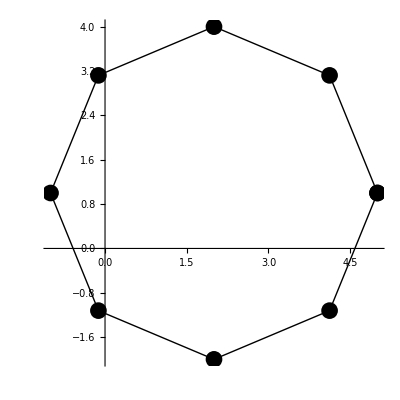

```mathematica
pad=2+I+3cPath[8];
cPlotPath[pad,AxesOrigin->{0,0}]
```

```mathematica
f[z_]:=(z-2-2I)/((z-1)(z-2)(z-3))
g[z_]:=1/f[z]
1/(2π I)cContourIntegral[f'[z]/f[z],z,pad]
1/(2π I)cContourIntegral[g'[z]/g[z],z,pad]
Residue[f[z],{z,1}]
Residue[f[z],{z,2}]
Residue[f[z],{z,3}]
```

-2

2

-1/2-ⅈ

2 ⅈ

1/2-ⅈ

```mathematica
ClearAll[f]
f[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
Integrate[z f'[z]/f[z],{z,2,2+I}]-Integrate[z f'[z]/f[z],{z,0,2+I}]//N
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.+1.6307264337491272247061977852624818327001639744350376180560574377×10^-29 ⅈ}. NIntegrate obtained -597.21-1.5708 ⅈ and 92.9891 for the integral and error estimates.

-594.069-6.28319 ⅈ

```mathematica
ClearAll[f]
Integrate[f'[z]/f[z],z]
D[Log[f[z]],{z,1}]
```

Log[f[z]]

f'[z]/f[z]

### MFDS 1.3

### MFDS 1.4

### MFDS 1.5

### MFDS 1.6

### MFDS 1.7

```mathematica
Discriminant[4 x^3-a x-b,x,Method->"Modular"]
Discriminant[4 x^3-a x-b,x]/16
```

16 (a^3-27 b^2)

a^3-27 b^2

```mathematica
p=Solve[4 x^3-a x-b==0,x][[1,1,2]];
q=Solve[4 x^3-a x-b==0,x][[2,1,2]];
r=Solve[4 x^3-a x-b==0,x][[3,1,2]];
16((q-p)(r-q)(r-p))^2//FullSimplify
```

a^3-27 b^2

### MFDS 1.8

#### a)

```mathematica
ClearAll[w,p,wi];
w={2,1+3I};
wi=WeierstrassInvariants[w]//N//Chop;
p[z_]:=WeierstrassP[z,wi]
```

```mathematica
p''[w[[1]]]//N
6 WeierstrassE1[wi]^2-1/2 wi[[1]]//N//Chop
```

0.761992

0.761992

```mathematica
ClearAll[e1,e2,e3];
e1=WeierstrassE1[wi]//N;
e2=WeierstrassE2[wi]//N;
e3=WeierstrassE3[wi]//N;
```

```mathematica
p''[w[[1]]]//N//Chop
6 e1^2-1/2 wi[[1]]//N//Chop
6 e1^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
2(e1-e2)(e1-e3)//N//Chop
```

0.761992

0.761992

0.761992

«1 more identical outputs»

```mathematica
6 e1^2-1/2 wi[[1]]//N//Chop
6 e1^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
6 e1^2 +2e1 e3 +2e1 e2+2e2 e3//N//Chop
6 e1^2 +2e1 e3 +2e2 (e1+e3)//N//Chop
6 e1^2 +2e1 e3 -2 e2^2//N//Chop
6 e1^2 -2 e1^2-2e1(-e1-e3) -2 e2^2//N//Chop
6 e1^2 -2 e1^2-2e1 e2 -2 e2^2//N//Chop
6 e1^2+2e1 e2 -2 e1^2-4e1 e2 -2 e2^2//N//Chop
6 e1^2+2e1 e2 -2(-e1-e2)^2//N//Chop
4 e1^2+2 e1^2+2e1 e2 -2(-e1-e2)^2//N//Chop
4 e1^2-2e1 (-e1-e2) -2 e3^2//N//Chop
4 e1^2-2e1 e3 -2 e3^2//N//Chop
2(2e1+e3)(e1-e3)//N//Chop
2(e1-e2)(e1-e3)//N//Chop
```

0.761992

0.761992

0.761992

«11 more identical outputs»

#### b)

```mathematica
ClearAll[e1,e2,e3];
e1=WeierstrassE1[wi]//N;
e2=WeierstrassE2[wi]//N;
e3=WeierstrassE3[wi]//N;
```

```mathematica
p''[w[[1]]+w[[2]]]//N//Chop
6 e2^2-1/2 wi[[1]]//N//Chop
6 e2^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
2(e2-e1)(e2-e3)//N//Chop
```

-0.101763

-0.101763

-0.101763

«1 more identical outputs»

```mathematica
p''[w[[2]]]//N//Chop
6 e3^2-1/2 wi[[1]]//N//Chop
6 e3^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
2(e3-e1)(e3-e2)//N//Chop
```

0.117495

0.117495

0.117495

«1 more identical outputs»

### MFDS 1.9

```mathematica
ClearAll[w,p,wi];
w={2,1+3I};
wi=WeierstrassInvariants[w]//N//Chop;
g2=WeierstrassInvariantG2[w]//N//Chop;
g3=WeierstrassInvariantG3[w]//N//Chop;
p[z_]:=WeierstrassP[z,wi]
v=0.6+0.2I;
```

```mathematica
p[2v]//N
((p[v]^2+1/4 g2)^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)
1/4(p''[v]/p'[v])^2-2p[v]
1/4((12 p[v]^2-g2)/(2p'[v]))^2-2p[v]
```

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

«1 more identical outputs»

```mathematica
p[2v]
1/4(p''[v]/p'[v])^2-2p[v]
1/4((6 p[v]^2-1/2 g2)^2)/(4 p[v]^3-g2 p[v]-g3)-2p[v]
1/4(((6 p[v]^2-1/2 g2)^2-4 2p[v](4 p[v]^3-g2 p[v]-g3))/(4 p[v]^3-g2 p[v]-g3))
1/4(((6 p[v]^2-1/2 g2)^2-32 p[v]^4+8g2 p[v]^2+8g3 p[v])/(4 p[v]^3-g2 p[v]-g3))
1/4((36 p[v]^4-6g2 p[v]^2+1/4 g2^2-32 p[v]^4+8g2 p[v]^2+8g3 p[v])/(4 p[v]^3-g2 p[v]-g3))
(9 p[v]^4-3/2 g2 p[v]^2+1/16 g2^2-8 p[v]^4+2g2 p[v]^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)
(p[v]^4+1/2 g2 p[v]^2+1/16 g2^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)


((p[v]^2+1/4 g2)^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)
```

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

«6 more identical outputs»

### MFDS 1.10

```mathematica
ClearAll[f]
RSolve[f[x+ω]==A f[x],f[x],x]
```

{{f[x]→A^(-1+x/ω) C[1]}}

### MFDS 1.11

#### (2).

```mathematica
1/z+Sum[(1/(z+m)-1/m)+(1/(z-m)+1/m),{m,1,Infinity}]//FullSimplify
```

π Cot[π z]

```mathematica
ClearAll[q]
q[z_]:=Exp[2 π ⅈ z]
π ⅈ - 2 π ⅈ Sum[q[z]^m,{m,0,Infinity}]//FullSimplify
```

π Cot[π z]

#### (3).

```mathematica
(-1)^j j!(1/z^(j+1)+Sum[(1/(z+m))^(j+1)+(1/(z-m))^(j+1),{m,1,Infinity}])/.{z:>I,j:>5}//N
```

121.866

```mathematica
-(2π ⅈ)^(j+1)Sum[n^j ⅇ^(2 π ⅈ z n),{n,1,Infinity}]/.{z:>I,j:>5}//N
```

121.866

### MFDS 1.12

```mathematica
WeierstrassInvariantG2[{.45,1+I}]
16WeierstrassInvariantG2[{.90,2+2I}]

60 nEisensteinG2K[2,{.90,2+2I}]//Chop
```

197.963+0.0403866 ⅈ

197.963+0.0403866 ⅈ

197.963+0.0403866 ⅈ

```mathematica
1/60 WeierstrassInvariantG2[{1/2,(2+1.15I)/2}]//N//Chop;
G1[2,2+1.15I]//Chop;
```

```mathematica
nEisensteinG2K[2,1.2(2+1.15I)]//Chop
1.2^-4 nEisensteinG2K[2,{1/1.2,(2+1.15I)}]//Chop

1.2^4 nEisensteinG2K[2,1.2(2+1.15I)]//Chop
nEisensteinG2K[2,{1/1.2,(2+1.15I)}]//Chop
```

2.0926+0.0522459 ⅈ

2.0926+0.0522459 ⅈ

4.33921+0.108337 ⅈ

4.33921+0.108337 ⅈ

#### tmp-1:

```mathematica
ClearAll[k,t]
G[k_,t_]:=2Zeta[2k]+2 (2 Pi I)^(2k)/((2k-1)!)Sum[DivisorSigma[2k-1,n]Exp[2 Pi I t n],{n,1,Infinity}]
G1[k_,t_]:=2Zeta[2k](1+2/Zeta[1-2k] Sum[DivisorSigma[2k-1,n]Exp[2 Pi I t n],{n,1,Infinity}])

ClearAll[g2,m,t,r]
g2[2,t_]=WeierstrassInvariantG2[{1/2,t/2}]/60;
g2[3,t_]=WeierstrassInvariantG3[{1/2,t/2}]/140;
g2[m_,t_]:=3Sum[(2r-1)(2m-2r-1)g2[r,t]g2[m-r,t],{r,2,m-2}]/((2m+1)(m-3)(2m-1))
```

```mathematica
WeierstrassInvariantG2[{1/2,1/2I}]/60//N
WeierstrassInvariantG3[{1/2,1/2I}]/140//N
(WeierstrassInvariantG2[{1/2,1/2I}]/60)^2 3/7//N
(WeierstrassInvariantG2[{1/2,1/2I}]/60)^3(2 9)/(13  11)//N
```

3.15121

0.

4.25577

3.93885

```mathematica
G[8,1.3+1.2I]//N
```

1.94692-0.0552305 ⅈ

```mathematica
G1[8,1.3+1.2I]//N
```

1.94692-0.0552305 ⅈ

```mathematica
g2[8,1.3+1.2I]//N
```

1.94692-0.0552305 ⅈ

#### tmp-2:

```mathematica
r=Exp[1/3 Pi I];
r^4//N
r^6//N
r^8//N
```

-0.5-0.866025 ⅈ

1.

-0.5+0.866025 ⅈ

```mathematica
WeierstrassInvariantG3[{1,r}]/140//N//Chop
WeierstrassInvariantG3[{1,r^2}]/140//N//Chop
WeierstrassInvariantG3[{1,r^2+1}]/140//N//Chop
```

0.0916099

0.0916099

0.0916099

```mathematica
WeierstrassInvariantG3[{1,-0.5+0.25I}]/140//N//Chop
WeierstrassInvariantG3[{1,0.5+0.25I}]/140//N//Chop
```

-3.83332

-3.83332

```mathematica
(WeierstrassInvariantG2[{1,r}]/60)^2 3/7//N
(WeierstrassInvariantG2[{1,r^2}]/60)^2 3/7//N
(WeierstrassInvariantG2[{1,0.5+0.75I}]/60)^2 3/7(0.5+0.75I)^8//N 
(WeierstrassInvariantG2[{1,-1/(0.5+0.75I)}]/60)^2 3/7//N
```

2.32054×10^-33+6.76824×10^-33 ⅈ

-7.85599×10^-33-5.51128×10^-33 ⅈ

-0.0000278365+0.00332641 ⅈ

-0.0000278365+0.00332641 ⅈ

#### tmp-3:

```mathematica
ClearAll[g2,m,t,r]
g2[2,t_]=WeierstrassInvariantG2[{1,t}]/60;
g2[3,t_]=WeierstrassInvariantG3[{1,t}]/140;
g2[m_,t_]:=3Sum[(2r-1)(2m-2r-1)g2[r,t]g2[m-r,t],{r,2,m-2}]/((2m+1)(m-3)(2m-1))
```

```mathematica
3/7 g2[2,.15I]^2//Chop
g2[4,.15I]//Chop
```

30607.4

30607.4

```mathematica
π^4 4/3 60
Zeta[4]
```

80 π^4

π^4/90

```mathematica
g2[4,(1.2I)]//N//Chop
g2[4,2(1.2I)]//N//Chop
```

0.00998403

0.00784542

```mathematica
G[4,0.15I]//N//Chop
```

7.83573×10^6

### MFDS 1.13

#### TEMP

```mathematica
g2[{w1_,w3_}]:=WeierstrassInvariantG2[{w1,w3}/2]
g3[{w1_,w3_}]:=WeierstrassInvariantG3[{w1,w3}/2]
```

```mathematica
g2[{1,2I}]//N//Chop
g2[{1,1.2I}]//N//Chop
g2[{1,1.4I}]//N//Chop
g3[{1,2I}]//N//Chop
g3[{1,1.2I}]//N//Chop
g3[{1,1.4I}]//N//Chop
```

129.987

146.525

134.6

284.355

207.207

263.03

```mathematica
g2s[t_]:=4/3 Pi^4(1+240Sum[DivisorSigma[3,n]Exp[2Pi I t n],{n,1,21}])
g2s[t_]:=4/3 Pi^4 240Sum[nDivisorSigma[3,n]Exp[2Pi I t n],{n,0,21}]
g3s[t_]:=8/27 Pi^6(1-504Sum[DivisorSigma[5,n]Exp[2Pi I t n],{n,1,21}])
g3s[t_]:=8/27 Pi^6*-504Sum[nDivisorSigma[5,n]Exp[2Pi I t n],{n,0,21}]
g2s[2I]//N//Chop
g2s[1.2I]//N//Chop
g2s[1.4I]//N//Chop
g3s[2I]//N//Chop
g3s[1.2I]//N//Chop
g3s[1.4I]//N//Chop
```

129.987

146.525

134.6

284.355

207.207

263.03

```mathematica
d[t_]:=g2s[t]^3-27 g3s[t]^2
d[2I]//N//Chop
d[1.2I]//N//Chop
d[1.4I]//N//Chop
```

13201.3

1.9866×10^6

570595.

```mathematica
ds[t_]:=(2Pi)^12 Sum[RamanujanTau[n]Exp[2Pi I t n],{n,0,21}]
ds[2I]//N//Chop
ds[1.2I]//N//Chop
ds[1.4I]//N//Chop
```

13201.3

1.9866×10^6

570595.

```mathematica
g2s[t_]:=4/3 Pi^4 240Sum[nDivisorSigma[3,n]Exp[2Pi I t n],{n,0,21}]
g3s[t_]:=-8/27 Pi^6 504Sum[nDivisorSigma[5,n]Exp[2Pi I t n],{n,0,21}]

rt[n_]:=8000nCauchyProduct[nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&],nDivisorSigma[3,#]&][n]-147nCauchyProduct[nDivisorSigma[5,#]&,nDivisorSigma[5,#]&][n]

d[t_]:=g2s[t]^3-27 g3s[t]^2
ds[t_]:=(2Pi)^12 Sum[RamanujanTau[n]Exp[2Pi I t n],{n,1,21}]
ds2[t_]:=(2Pi)^12 Sum[rt[n]Exp[2Pi I t n],{n,1,21}]

d[1.47I]//N//Chop
ds[1.47I]//N//Chop
ds2[1.47I]//N//Chop
```

368024.

368024.

368024.

```mathematica
(4/3 Pi^4 240)^3
27(-8/27 Pi^6 504)^2
```

32768000 π^12

602112 π^12

```mathematica
(4/3 Pi^4 240)^3/(2Pi)^12
27(-8/27 Pi^6 504)^2/(2Pi)^12
```

8000

147

```mathematica
ClearAll[q,f,f2]
q[t_]:=Exp[2 Pi I t]
f[t_]:=4/3 Pi^4(1+240Sum[n^3 q[t]^n/(1-q[t]^n),{n,1,201}])
f2[t_]:=4/3 Pi^4(1+240Sum[n^3 q[t]^n/(1-q[t]^n),{n,1,201}])
g2s[1.47I]//N//Chop
f[1.47I]//N//Chop
```

132.919

General::munfl: (0.0000974392+0. ⅈ)^77 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.0000974392+0. ⅈ)^78 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

132.919

```mathematica
(2n-1)^5//Expand
```

-1+10 n-40 n^2+80 n^3-80 n^4+32 n^5

```mathematica
ClearAll[n]
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)//Simplify
Expand[(((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)//Simplify),x]
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>1
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>2
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>3
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>4
```

(-1+2 n)^5 x^(-9+2 n) (x^8+x^(16 n)-x^(7+2 n)+x^(6+4 n)-x^(5+6 n)+x^(4+8 n)-x^(3+10 n)+x^(2+12 n)-x^(1+14 n))

(-1+2 n)^5 x^(-1+2 n)-(-1+2 n)^5 x^(-2+4 n)+(-1+2 n)^5 x^(-3+6 n)-(-1+2 n)^5 x^(-4+8 n)+(-1+2 n)^5 x^(-5+10 n)-(-1+2 n)^5 x^(-6+12 n)+(-1+2 n)^5 x^(-7+14 n)-(-1+2 n)^5 x^(-8+16 n)+(-1+2 n)^5 x^(-9+18 n)

x-x^2+x^3-x^4+x^5-x^6+x^7-x^8+x^9

243 x^3-243 x^6+243 x^9-243 x^12+243 x^15-243 x^18+243 x^21-243 x^24+243 x^27

3125 x^5-3125 x^10+3125 x^15-3125 x^20+3125 x^25-3125 x^30+3125 x^35-3125 x^40+3125 x^45

16807 x^7-16807 x^14+16807 x^21-16807 x^28+16807 x^35-16807 x^42+16807 x^49-16807 x^56+16807 x^63

```mathematica
(-1+2 n)^5 x^(-9+2 n) (x^8+x^(16 n)-x^(7+2 n)+x^(6+4 n)-x^(5+6 n)+x^(4+8 n)-x^(3+10 n)+x^(2+12 n)-x^(1+14 n))
x^(-9+2 n) (x^8+x^(16 n)-x^(7+2 n)+x^(6+4 n)-x^(5+6 n)+x^(4+8 n)-x^(3+10 n)+x^(2+12 n)-x^(1+14 n))//Expand
```

(-1+2 n)^5 x^(-9+2 n) (x^8+x^(16 n)-x^(7+2 n)+x^(6+4 n)-x^(5+6 n)+x^(4+8 n)-x^(3+10 n)+x^(2+12 n)-x^(1+14 n))

x^(-1+2 n)-x^(-2+4 n)+x^(-3+6 n)-x^(-4+8 n)+x^(-5+10 n)-x^(-6+12 n)+x^(-7+14 n)-x^(-8+16 n)+x^(-9+18 n)

```mathematica
n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand
-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand
64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand
```

n^5 x^n+n^5 x^(2 n)+n^5 x^(3 n)+n^5 x^(4 n)+n^5 x^(5 n)+n^5 x^(6 n)+n^5 x^(7 n)+n^5 x^(8 n)+n^5 x^(9 n)

-34 n^5 x^(2 n)-34 n^5 x^(4 n)-34 n^5 x^(6 n)-34 n^5 x^(8 n)-34 n^5 x^(10 n)-34 n^5 x^(12 n)-34 n^5 x^(14 n)-34 n^5 x^(16 n)-34 n^5 x^(18 n)

64 n^5 x^(4 n)+64 n^5 x^(8 n)+64 n^5 x^(12 n)+64 n^5 x^(16 n)+64 n^5 x^(20 n)+64 n^5 x^(24 n)+64 n^5 x^(28 n)+64 n^5 x^(32 n)+64 n^5 x^(36 n)

```mathematica
(n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand)/.n:>1
(n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand)/.n:>2
(n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand)/.n:>3
(n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand)/.n:>4
(n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand)/.n:>5
(n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^n//Expand)/.n:>6
DivisorSigma[5,4]
```

x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9

32 x^2+32 x^4+32 x^6+32 x^8+32 x^10+32 x^12+32 x^14+32 x^16+32 x^18

243 x^3+243 x^6+243 x^9+243 x^12+243 x^15+243 x^18+243 x^21+243 x^24+243 x^27

1024 x^4+1024 x^8+1024 x^12+1024 x^16+1024 x^20+1024 x^24+1024 x^28+1024 x^32+1024 x^36

3125 x^5+3125 x^10+3125 x^15+3125 x^20+3125 x^25+3125 x^30+3125 x^35+3125 x^40+3125 x^45

7776 x^6+7776 x^12+7776 x^18+7776 x^24+7776 x^30+7776 x^36+7776 x^42+7776 x^48+7776 x^54

1057

```mathematica
(-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand)/.n:>1
(-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand)/.n:>2
(-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand)/.n:>3
(-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand)/.n:>4
(-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand)/.n:>5
(-34 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(2n)//Expand)/.n:>6
```

-34 x^2-34 x^4-34 x^6-34 x^8-34 x^10-34 x^12-34 x^14-34 x^16-34 x^18

-1088 x^4-1088 x^8-1088 x^12-1088 x^16-1088 x^20-1088 x^24-1088 x^28-1088 x^32-1088 x^36

-8262 x^6-8262 x^12-8262 x^18-8262 x^24-8262 x^30-8262 x^36-8262 x^42-8262 x^48-8262 x^54

-34816 x^8-34816 x^16-34816 x^24-34816 x^32-34816 x^40-34816 x^48-34816 x^56-34816 x^64-34816 x^72

-106250 x^10-106250 x^20-106250 x^30-106250 x^40-106250 x^50-106250 x^60-106250 x^70-106250 x^80-106250 x^90

-264384 x^12-264384 x^24-264384 x^36-264384 x^48-264384 x^60-264384 x^72-264384 x^84-264384 x^96-264384 x^108

```mathematica
(64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand)/.n:>1
(64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand)/.n:>2
(64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand)/.n:>3
(64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand)/.n:>4
(64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand)/.n:>5
(64 n^5(Series[x/(1-x),{x,0,9}]//Normal)/.x:>x^(4n)//Expand)/.n:>6
```

64 x^4+64 x^8+64 x^12+64 x^16+64 x^20+64 x^24+64 x^28+64 x^32+64 x^36

2048 x^8+2048 x^16+2048 x^24+2048 x^32+2048 x^40+2048 x^48+2048 x^56+2048 x^64+2048 x^72

15552 x^12+15552 x^24+15552 x^36+15552 x^48+15552 x^60+15552 x^72+15552 x^84+15552 x^96+15552 x^108

65536 x^16+65536 x^32+65536 x^48+65536 x^64+65536 x^80+65536 x^96+65536 x^112+65536 x^128+65536 x^144

200000 x^20+200000 x^40+200000 x^60+200000 x^80+200000 x^100+200000 x^120+200000 x^140+200000 x^160+200000 x^180

497664 x^24+497664 x^48+497664 x^72+497664 x^96+497664 x^120+497664 x^144+497664 x^168+497664 x^192+497664 x^216

```mathematica
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>1
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>2
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>3
((2n-1)^5(Series[x/(1+x),{x,0,9}]//Normal)/.x:>x^(2n-1)//Expand)/.n:>4
```

x-x^2+x^3-x^4+x^5-x^6+x^7-x^8+x^9

243 x^3-243 x^6+243 x^9-243 x^12+243 x^15-243 x^18+243 x^21-243 x^24+243 x^27

3125 x^5-3125 x^10+3125 x^15-3125 x^20+3125 x^25-3125 x^30+3125 x^35-3125 x^40+3125 x^45

16807 x^7-16807 x^14+16807 x^21-16807 x^28+16807 x^35-16807 x^42+16807 x^49-16807 x^56+16807 x^63

```mathematica
1+32+1024-34-1088+64
1+32+243+7776-34-8262
```

-1

-244

#### Pre-amble

```mathematica
t=0.8I;
(1.7)^4 nEisensteinG2K[2,1.7t]//Chop
nEisensteinG2K[2,{1/1.7,t}]//Chop
```

18.9247

18.9247

```mathematica
1/120 nDivisorSigma[7,12]
nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&][12]
```

9032611/30

9032611/30

#### Ramanujan Tau

```mathematica
Series[q Product[(1-q^n)^24,{n,1,Infinity}],{q,0,15}]
```

q-24 q^2+252 q^3-1472 q^4+4830 q^5-6048 q^6-16744 q^7+84480 q^8-113643 q^9-115920 q^10+534612 q^11-370944 q^12-577738 q^13+401856 q^14+1217160 q^15+O[q]^16

```mathematica
RamanujanTau[#]&/@Range[15]
```

{1,-24,252,-1472,4830,-6048,-16744,84480,-113643,-115920,534612,-370944,-577738,401856,1217160}

```mathematica
RamanujanTau[3]RamanujanTau[5]
```

1217160

```mathematica
Table[8000nCauchyProduct[nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&],nDivisorSigma[3,#]&][k]-147nCauchyProduct[nDivisorSigma[5,#]&,nDivisorSigma[5,#]&][k],{k,1,15}]
```

{1,-24,252,-1472,4830,-6048,-16744,84480,-113643,-115920,534612,-370944,-577738,401856,1217160}

```mathematica
12 nCauchyProduct[nDivisorSigma[1,#]&,nDivisorSigma[1,#]&][12]
5nDivisorSigma[3,12]-(6 12-1)nDivisorSigma[1,12]
```

8204

8232

```mathematica
f[t_]:=4/3 π^4(1+240Sum[DivisorSigma[3,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}])
f[1+2/3 I]//N
f[1+2/3 I]//N
```

670.255

670.255

```mathematica
WeierstrassInvariantG2[{1,2(1+2/3 I)}]//N//Chop
```

8.56637

```mathematica
f[12I]//N
```

129.879

```mathematica
Sum[DivisorSigma[3,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}]
```

```mathematica
ClearAll[t]
t=1+(2/3)I;
4/3 π^4(1+240Sum[DivisorSigma[3,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}])//N//Chop
WeierstrassInvariantG2[{1,1+2/3I}/2]//N//Chop
```

670.255

670.255

```mathematica
(1+240Sum[DivisorSigma[3,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}])^2//N//Chop
1+480Sum[DivisorSigma[7,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}]//N//Chop
1+480Sum[DivisorSigma[3,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}]+240^2(Sum[DivisorSigma[3,k] ⅇ^(2 π ⅈ k t),{k,1,Infinity}])^2//N//Chop
```

26.632

26.632

26.632

```mathematica
nDivisorSigma[7,12]
120nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&][12]
```

36130444

36130444

```mathematica
nDivisorSigma[7,100]
120nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&][100]
```

100788643610263

100788643610263

```mathematica
240^2/480
```

120

```mathematica
nDivisorSigma[7,3]/120
nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&][3]
```

547/30

547/30

```mathematica
ClearAll[q,n]
Series[Product[1/(1-q^n),{n,1,Infinity}],{q,0,10}]
```

1+q+2 q^2+3 q^3+5 q^4+7 q^5+11 q^6+15 q^7+22 q^8+30 q^9+42 q^10+O[q]^11

```mathematica
240/12
```

20

#### Ramanujan: On Certain Arithmetical Functions

```mathematica
nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&][20]
```

215015773/20

```mathematica
(Gamma[4]Gamma[4])/Gamma[8](Zeta[4]Zeta[4])/Zeta[8] nDivisorSigma[7,20]+(Zeta[-2]Zeta[-2])/Zeta[6] 20nDivisorSigma[5,20]
```

215015773/20

```mathematica
nDivisorSigma[7,20]/120
```

215015773/20

```mathematica
D[(n q^n)/(1-q^n),{q,1}]//FullSimplify
```

(n^2 q^(-1+n))/((-1+q^n)^2)

```mathematica
l[q_]:=1-24Sum[(n q^n)/(1-q^n),{n,1,Infinity}]
lp[q_]:=24Sum[(n^2 q^(n-1))/((1-q^n)^2),{n,1,Infinity}]
m[q_]:=1+240Sum[(n^3 q^n)/(1-q^n),{n,1,Infinity}]
 lp[Exp[2 π ⅈ 0.32I]]//N//Chop
(l[Exp[2 π ⅈ 0.32I]]^2-m[Exp[2 π ⅈ 0.32I]])/(12 2 π ⅈ 0.32I)//N//Chop
```

50.3762

3.35502

```mathematica
l[q]^2//FullSimplify
```

(1-24 ∑_(n=1)^∞ (n q^n)/(1-q^n))^2

```mathematica
24^2
```

576

```mathematica
-48((n q^n)/(1-q^n))^1+576 ((n q^n)/(1-q^n))^2-240((n^3 q^n)/(1-q^n))^1//FullSimplify
240((n q^n)/(1-q^n))^2//FullSimplify
```

(48 n q^n (-1-5 n^2+(1+n (12+5 n)) q^n))/((-1+q^n)^2)

(240 n^2 q^(2 n))/((-1+q^n)^2)

```mathematica
With[{q=Exp[2 Pi I 0.2I]},Sum[(48 n q^n (-1-5 n^2+(1+n (12+5 n)) q^n))/((-1+q^n)^2),{n,1,Infinity}]]
```

∑_(n=1)^∞ (48 (0.28461+0. ⅈ)^n n (-1-5 n^2+(0.28461+0. ⅈ)^n (1+n (12+5 n))))/((-1+(0.28461+0. ⅈ)^n)^2)

```mathematica
With[{q=Exp[2 Pi I 0.2I]},Sum[(240 n^2 q^(2 n))/((-1+q^n)^2),{n,1,Infinity}]]
```

∑_(n=1)^∞ (240 (0.28461+0. ⅈ)^(2 n) n^2)/((-1+(0.28461+0. ⅈ)^n)^2)

```mathematica
1*-72+-24 * -24 +-72*1
```

432

```mathematica
(432-2160)/12
```

-144

```mathematica
D[-288 q^6,{q,1}]/q
```

-1728 q^4

```mathematica
ClearAll[p,q]
p[q_]:=1-24Sum[DivisorSigma[1,n] q^n,{n,1,Infinity}]
Table[-24nDivisorSigma[1,n],{n,0,12}]
```

{1,-24,-72,-96,-168,-144,-288,-192,-360,-312,-432,-288,-672}

```mathematica
((4 Pi^4)/3 240)^3
```

32768000 π^12

```mathematica
27((4 Pi^4)/3 240)^2
```

2764800 π^8

```mathematica
RamanujanTau[#]&/@Range[15]
```

{1,-24,252,-1472,4830,-6048,-16744,84480,-113643,-115920,534612,-370944,-577738,401856,1217160}

```mathematica
l1=Table[nDivisorSigma[3,n],{n,0,12}];
l2=ListConvolve[l1,l1,{1,-1},0][[1;;12]];
l3=8000ListConvolve[l2,l1,{1,-1},0][[1;;12]]
```

{1/1728,5/12,415/4,29435/3,2756765/12,5362105/2,19915105,325482430/3,1886436575/4,20662983785/12,10979708145/2,15655862755}

```mathematica
l4=Table[nDivisorSigma[5,n],{n,0,12}];
l5=147ListConvolve[l4,l4,{1,-1},0][[1;;12]]
```

{1/1728,-7/12,511/4,28679/3,2774429/12,5352445/2,19921153,325532662/3,1886098655/4,20664347501/12,10979939985/2,15655328143}

```mathematica
l3-l5
```

{0,1,-24,252,-1472,4830,-6048,-16744,84480,-113643,-115920,534612}

```mathematica
2000/25
```

80

```mathematica
Table[nCauchyProduct[2^#&,2^#&][k],{k,0,6}]
```

{1,4,12,32,80,192,448}

```mathematica
Table[8000nCauchyProduct[nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&],nDivisorSigma[3,#]&][k]-147nCauchyProduct[nDivisorSigma[5,#]&,nDivisorSigma[5,#]&][k],{k,1,15}]
```

```mathematica
240^3 Table[nCauchyProduct[nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&],nDivisorSigma[3,#]&][k],{k,0,10}]
```

{1,720,179280,16954560,396974160,4632858720,34413301440,187477879680,814940600400,2975469665040,9486467837280}

```mathematica
504^2 Table[nCauchyProduct[nDivisorSigma[5,#]&,nDivisorSigma[5,#]&][k],{k,0,10}]
```

{1,-1008,220752,16519104,399517776,4624512480,34423752384,187506813312,814794618960,2975666040144,9486668147040}

```mathematica
8000/19200+147/252
```

1

```mathematica
-147 27
```

-3969

```mathematica
(4/3)^3
(8/27)^2
```

64/27

64/729

```mathematica
FactorInteger[240]
FactorInteger[504]
```

{{2,4},{3,1},{5,1}}

{{2,3},{3,2},{7,1}}

```mathematica
2^10 5/9
(2^9 7)/3
```

5120/9

3584/3

#### tmp

```mathematica
Table[8000nCauchyProduct[nCauchyProduct[nDivisorSigma[3,#]&,nDivisorSigma[3,#]&],nDivisorSigma[3,#]&][k]-147nCauchyProduct[nDivisorSigma[5,#]&,nDivisorSigma[5,#]&][k],{k,1,15}]
```

{1,-24,252,-1472,4830,-6048,-16744,84480,-113643,-115920,534612,-370944,-577738,401856,1217160}

```mathematica
Table[120960nCauchyProduct[nCauchyProduct[nDivisorSigma[2,#]&,nDivisorSigma[3,#]&],nDivisorSigma[5,#]&][k],{k,1,15}]
```

{-1,259,136742,5876355,96684166,917149150,6050046766,30736888691,128325650021,459459245918,1453699741702,4155923456574,10910397454006,26654379529286,61176234809980}

```mathematica
Table[192nCauchyProduct[nCauchyProduct[nDivisorSigma[1,#]&,nDivisorSigma[1,#]&],nDivisorSigma[1,#]&][k],{k,1,15}]
```

{1,-21,52,1327,6582,21372,54824,119415,235933,425106,722652,1166284,1798622,2695224,3881208}

```mathematica
I^(1/I)//N//Chop
```

4.81048

```mathematica
Exp[Pi/2]//N
```

4.81048

```mathematica
DivisorSum[64,LiouvilleLambda[#]&]
```

1

### MFDS 1.14

#### Preamble-1

```mathematica
(1^5+2^5+3^5+4^5+6^5+12^5)-32(1^5+2^5+3^5+6^5)-2(1^5+2^5+3^5+6^5)+2 2^5(1^5+3^5);
(1^5+2^5+3^5+4^5+6^5+8^5+12^5+24^5)-32(1^5+2^5+3^5+4^5+6^5+12^5)-2(1^5+2^5+3^5+4^5+6^5+12^5)+2 2^5(1^5+2^5+3^5+6^5);
(1^5+2^5+3^5+4^5+6^5+8^5+12^5+24^5)-34(1^5+2^5+3^5+4^5+6^5+12^5)+64(1^5+2^5+3^5+6^5)
```

-244

```mathematica
(1^5+3^5+7^5+21^5)
```

4101152

#### Preamble-2

```mathematica
ClearAll[f,g,h]
g[n_]:=DivisorSigma[5,n]/;IntegerQ[n]
g[n_]:=0/;Not[IntegerQ[n]]
k[n_]:=g[n]-34g[n/2]+64g[n/4]

f[n_]:=Total[Select[Divisors[n],OddQ]^5]/;Mod[n,2]==1
f[n_]:=-Total[Select[Divisors[n],OddQ]^5]/;Mod[n,2]==0

h[n_]:=g[n]-32g[n/2]-2g[n/2]+2 32g[n/4]/;Mod[n,4]==0
h[n_]:=g[n]-32g[n/2]-2g[n/2]/;Mod[n,4]==2
h[n_]:=g[n]/;(Mod[n,4]==1||Mod[n,4]==3)

Table[{n,f[n],h[n],k[n]},{n,1,21}]//tf
```

1 | 1 | 1 | 1
2 | -1 | -1 | -1
3 | 244 | 244 | 244
4 | -1 | -1 | -1
5 | 3126 | 3126 | 3126
6 | -244 | -244 | -244
7 | 16808 | 16808 | 16808
8 | -1 | -1 | -1
9 | 59293 | 59293 | 59293
10 | -3126 | -3126 | -3126
11 | 161052 | 161052 | 161052
12 | -244 | -244 | -244
13 | 371294 | 371294 | 371294
14 | -16808 | -16808 | -16808
15 | 762744 | 762744 | 762744
16 | -1 | -1 | -1
17 | 1419858 | 1419858 | 1419858
18 | -59293 | -59293 | -59293
19 | 2476100 | 2476100 | 2476100
20 | -3126 | -3126 | -3126
21 | 4101152 | 4101152 | 4101152

#### Preamble-3

```mathematica
ClearAll[f,g,h]
g[n_]:=DivisorSigma[5,n]/;IntegerQ[n]
g[n_]:=0/;Not[IntegerQ[n]]
k[n_]:=g[n]-34g[n/2]+64g[n/4]

f[n_]:=Total[Select[Divisors[n],OddQ]^5]/;Mod[n,2]==1
f[n_]:=-Total[Select[Divisors[n],OddQ]^5]/;Mod[n,2]==0

h[n_]:=g[n]-32g[n/2]-2g[n/2]+2 32g[n/4]/;Mod[n,4]==0
h[n_]:=g[n]-32g[n/2]-2g[n/2]/;Mod[n,4]==2
h[n_]:=g[n]/;(Mod[n,4]==1||Mod[n,4]==3)

Table[{n,f[n],h[n],k[n]},{n,1,21}]//tf
```

1 | 1 | 1 | 1
2 | -1 | -1 | -1
3 | 244 | 244 | 244
4 | -1 | -1 | -1
5 | 3126 | 3126 | 3126
6 | -244 | -244 | -244
7 | 16808 | 16808 | 16808
8 | -1 | -1 | -1
9 | 59293 | 59293 | 59293
10 | -3126 | -3126 | -3126
11 | 161052 | 161052 | 161052
12 | -244 | -244 | -244
13 | 371294 | 371294 | 371294
14 | -16808 | -16808 | -16808
15 | 762744 | 762744 | 762744
16 | -1 | -1 | -1
17 | 1419858 | 1419858 | 1419858
18 | -59293 | -59293 | -59293
19 | 2476100 | 2476100 | 2476100
20 | -3126 | -3126 | -3126
21 | 4101152 | 4101152 | 4101152

```mathematica
k[12]
```

-244

#### Preamble-4

```mathematica
ClearAll[g,f]
g[n_]:=DivisorSigma[5,n]/;IntegerQ[n]
g[n_]:=0/;Not[IntegerQ[n]]
f[n_]:=g[n]-34g[n/2]+64g[n/4]
Table[f[n],{n,1,21}]
```

{1,-1,244,-1,3126,-244,16808,-1,59293,-3126,161052,-244,371294,-16808,762744,-1,1419858,-59293,2476100,-3126,4101152}

#### Test-1: F(x)

```mathematica
Rest[CoefficientList[Sum[(Series[n^5 x^n/(1+x^n)/.n:>a,{x,0,21}]//Normal),{a,1,21,2}],x]];
Sum[(Series[n^5 x^n/(1+x^n)/.n:>a,{x,0,21}]//Normal),{a,1,21,2}]
```

x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21

```mathematica
x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21
```

#### Test-2: G(x)

```mathematica
Sum[Expand[(n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^n)-(34 n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^(2n))+(64 n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^(4n)),x]/.n:>a,{a,1,21}][[1;;21]]
```

x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21

#### temp-1: F(x)

```mathematica
Sum[(Series[(2n-1)^5 x^(2n-1)/(1+x^(2n-1))/.n:>a,{x,0,21}]//Normal),{a,1,21}];
Sum[(Series[(2n-1)^5(x^(2n-1)-x^(4n-2))/(1-x^(4n-2))/.n:>a,{x,0,21}]//Normal),{a,1,21}]
```

x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21

#### temp-2: G(x)-34G(x^2)+64G(x^4)

```mathematica
Sum[(Series[n^5((x^n+x^(2n)+x^(3n)+x^(4n))/(1-x^(4n))+(-34 x^(2n)-34 x^(4n))/(1-x^(4n))+(64 x^(4n))/(1-x^(4n)))/.n:>a,{x,0,21}]//Normal),{a,1,21}];
Sum[(Series[n^5((x^n-33 x^(2n)+x^(3n)+31 x^(4n))/(1-x^(4n)))/.n:>a,{x,0,21}]//Normal),{a,1,21}];
Sum[(Series[-31 n^5-n^5 1/(1+x^n)+32 n^5 1/(1+x^(2 n))/.n:>a,{x,0,21}]//Normal),{a,1,21}]
```

x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21

#### Uitwerking

```mathematica
(Series[Sum[(2n-1)^5(x^(2n-1)-x^(4n-2))/(1-x^(4n-2))/.n:>a,{a,1,25}],{x,0,48}]//Normal)
```

x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21-161052 x^22+6436344 x^23-244 x^24+9768751 x^25-371294 x^26+14408200 x^27-16808 x^28+20511150 x^29-762744 x^30+28629152 x^31-x^32+39296688 x^33-1419858 x^34+52541808 x^35-59293 x^36+69343958 x^37-2476100 x^38+90595736 x^39-3126 x^40+115856202 x^41-4101152 x^42+147008444 x^43-161052 x^44+185349918 x^45-6436344 x^46+229345008 x^47-244 x^48

```mathematica
Table[{n,DivisorSum[n,If[OddQ[#],#^5,0]&](-1)^(n+1),If[OddQ[n],DivisorSum[n,If[OddQ[#],#^5,0]&],"-"],If[EvenQ[n],DivisorSum[n,If[OddQ[#],#^5,0]&],"-"],If[Mod[n,4]==0,DivisorSum[n,If[OddQ[#],#^5,0]&],"-"]},{n,1,11}]//tf
```

1 | 1 | 1 | - | -
2 | -1 | - | 1 | -
3 | 244 | 244 | - | -
4 | -1 | - | 1 | 1
5 | 3126 | 3126 | - | -
6 | -244 | - | 244 | -
7 | 16808 | 16808 | - | -
8 | -1 | - | 1 | 1
9 | 59293 | 59293 | - | -
10 | -3126 | - | 3126 | -
11 | 161052 | 161052 | - | -

#### temp-X

```mathematica
1^5+2^5+3^5+4^5+6^5+12^5-32(1^5+2^5+3^5+6^5)
1^5+2^5+3^5+4^5+6^5+12^5-32(1^5+2^5+3^5+6^5)-2(1^5+3^5)
1^5+2^5+3^5+4^5+6^5+12^5-32(1^5+2^5+3^5+6^5)-2(1^5+2^5+3^5+6^5)+2 2^5(1^5+3^5)
```

244

-244

-244

```mathematica
1^5+2^5+3^5+6^5-32(1^5+3^5)-2(1^5+3^5)
```

-244

```mathematica
Table[{n,DivisorSum[n,If[OddQ[#],#^5,0]&](-1)^(n+1),If[OddQ[n],DivisorSum[n,If[OddQ[#],#^5,0]&],"-"],If[EvenQ[n],DivisorSum[n,If[OddQ[#],#^5,0]&],"-"],If[Mod[n,4]==0,DivisorSum[n,If[OddQ[#],#^5,0]&],"-"]},{n,1,11}]//tf
```

1 | 1 | 1 | - | -
2 | -1 | - | 1 | -
3 | 244 | 244 | - | -
4 | -1 | - | 1 | 1
5 | 3126 | 3126 | - | -
6 | -244 | - | 244 | -
7 | 16808 | 16808 | - | -
8 | -1 | - | 1 | 1
9 | 59293 | 59293 | - | -
10 | -3126 | - | 3126 | -
11 | 161052 | 161052 | - | -

```mathematica
Sum[Expand[(n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^n),x]/.n:>a,{a,1,21}][[1;;21]];
Sum[Expand[(1 n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^(2n)),x]/.n:>a,{a,1,21}][[1;;21]];
Sum[Expand[(1 n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^(4n)),x]/.n:>a,{a,1,21}][[1;;21]];
Sum[Expand[(n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^n)-(34 n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^(2n))+(64 n^5(Series[x/(1-x),{x,0,21}]//Normal)/.x:>x^(4n)),x]/.n:>a,{a,1,21}][[1;;21]];
```

x^2+33 x^4+244 x^6+1057 x^8+3126 x^10+8052 x^12+16808 x^14+33825 x^16+59293 x^18+103158 x^20+161052 x^22+257908 x^24+371294 x^26+554664 x^28+762744 x^30+1082401 x^32+1419858 x^34+1956669 x^36+2476100 x^38+3304182 x^40+4101152 x^42

#### temp-Y

```mathematica
Sum[(Series[n^5 x^n/(1+x^n)/.n:>a,{x,0,21}]//Normal),{a,1,21,2}]
```

x-x^2+244 x^3-x^4+3126 x^5-244 x^6+16808 x^7-x^8+59293 x^9-3126 x^10+161052 x^11-244 x^12+371294 x^13-16808 x^14+762744 x^15-x^16+1419858 x^17-59293 x^18+2476100 x^19-3126 x^20+4101152 x^21

```mathematica
Sum[n^5 x^n/(1+x^n),{n,1,11}]//FullSimplify//N
```

x (1/(1.+x)+x (32./(1.+x^2)+(243. x)/(1.+x^3)+(1024. x^2)/(1.+x^4)+(3125. x^3)/(1.+x^5)+(7776. x^4)/(1.+x^6)+(16807. x^5)/(1.+x^7)+(32768. x^6)/(1.+x^8)+(59049. x^7)/(1.+x^9)+(100000. x^8)/(1.+x^10)+(161051. x^9)/(1.+x^11)))

```mathematica
Rest@CoefficientList[Series[Sum[n^5 x^n/(1+x^n),{n,1,48,2}],{x,0,48}]//Normal,x]
g[n_]:=DivisorSigma[5,n]/;IntegerQ[n]
g[n_]:=0/;Not[IntegerQ[n]] 
f[n_]:=g[n]-34 g[n/2]+64 g[n/4]
Table[f[n],{n,1,48}]
```

{1,-1,244,-1,3126,-244,16808,-1,59293,-3126,161052,-244,371294,-16808,762744,-1,1419858,-59293,2476100,-3126,4101152,-161052,6436344,-244,9768751,-371294,14408200,-16808,20511150,-762744,28629152,-1,39296688,-1419858,52541808,-59293,69343958,-2476100,90595736,-3126,115856202,-4101152,147008444,-161052,185349918,-6436344,229345008,-244}

{1,-1,244,-1,3126,-244,16808,-1,59293,-3126,161052,-244,371294,-16808,762744,-1,1419858,-59293,2476100,-3126,4101152,-161052,6436344,-244,9768751,-371294,14408200,-16808,20511150,-762744,28629152,-1,39296688,-1419858,52541808,-59293,69343958,-2476100,90595736,-3126,115856202,-4101152,147008444,-161052,185349918,-6436344,229345008,-244}

```mathematica
Table[DivisorSigma[1,Fibonacci[n]],{n,1,11}]
```

{1,1,3,4,6,15,14,32,54,72,90}

```mathematica
Divisors[120]
```

{1,2,3,4,5,6,8,10,12,15,20,24,30,40,60,120}

```mathematica
Integrate[(x-x^2)^n,{x,0,1},Assumptions->{Re[n]>-1}]
```

Gamma[1+n]^2/Gamma[2+2 n]

```mathematica
Gamma[2]^2/Gamma[4]
```

1/6

```mathematica
Exp[2 Pi I z n]/.{z:>1,n:>5}
```

1

```mathematica
ClearAll[f]
f[z_]:=Exp[2 Pi I z n]/(1-Exp[2 Pi I z n])
f[1]
f[I]//Apart
```

ⅇ^(2 ⅈ n π)/(1-ⅇ^(2 ⅈ n π))

1/(2 (-1+ⅇ^(n π)))-1/(2 (1+ⅇ^(n π)))

### MFDS 1.15

https://math.stackexchange.com/questions/3486679/regarding-proving-a-series-result-from-tom-m-apostol-modular-functions-and-diric

#### Preamble

```mathematica
nEisensteinG2K[3,{1,2I}]//N
nEisensteinG2K[3,{1,I/2}]//N
```

2.03111+0. ⅈ

-129.991+0. ⅈ

2. The Modular Group and Modular Functions

## 2.1 Möbius Transformations

## 2.2 The Modular Group

## 2.3 Fundamental Regions

## 2.4 Modular Functions

## 2.5 Special Values of J

## 2.6 Modular Functions as Rational Functions of J

## 2.7 Mapping Properties of J

## 2.8 Application to the Inversion Problem for Eisenstein Series

## 2.9Application to Picard’s Theorem

## Exercises

### MFDS 2.1A

```mathematica
ClearAll[a,b,c,d]
mA={{a,b},{c,d}};
mS={{0,-1},{1,0}};
mS//mf
Inverse[mS]//mf
```

(0 | -1
1 | 0)

(0 | 1
-1 | 0)

```mathematica
mA==mS.mA.Inverse[mS]
RowReduce[{{1,0,0,-1},{0,1,1,0},{0,1,1,0},{1,0,0,-1}}]
mAC={{a,b},{-b,a}};
mAC.mS
mS.mAC
```

{{a,b},{c,d}}=={{d,-c},{-b,a}}

{{1,0,0,-1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}

{{b,-a},{a,b}}

{{b,-a},{a,b}}

```mathematica
Clear[x,y]
Solve[x^2+y^2==1,{x,y},Integers]
```

{{x→-1,y→0},{x→0,y→-1},{x→0,y→1},{x→1,y→0}}

### MFDS 2.1B

```mathematica
ClearAll[a,b,c,d]
mA={{a,b},{c,d}};
mS={{0,-1},{1,0}};
mT ={{1,1},{0,1}};
(mS.mT)//mf
Inverse[(mS.mT)]//mf
```

(0 | -1
1 | 1)

(1 | 1
-1 | 0)

```mathematica
mA.(mS.mT)==(mS.mT).mA
RowReduce[{{0,1,1,0},{1,-1,0,-1},{1,0,1,-1},{0,1,1,0}}]
mAC={{-c+d,-c},{c,d}}

mAC.(mS.mT)
(mS.mT).mAC
```

{{b,-a+b},{d,-c+d}}=={{-c,-d},{a+c,b+d}}

{{1,0,1,-1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}

{{-c+d,-c},{c,d}}

{{-c,-d},{d,-c+d}}

{{-c,-d},{d,-c+d}}

```mathematica
Clear[x,y]
Solve[x^2-x y+y^2==1,{x,y},Integers]
mAC={{-c+d,-c},{c,d}}
```

{{x→-1,y→-1},{x→-1,y→0},{x→0,y→-1},{x→0,y→1},{x→1,y→0},{x→1,y→1}}

{{-c+d,-c},{c,d}}

```mathematica
{{0,1},{-1,-1}}.(mS.mT)//mf
(mS.mT).{{0,1},{-1,-1}}//mf

{{1,1},{-1,0}}.(mS.mT)//mf
(mS.mT).{{1,1},{-1,0}}//mf

{{-1,0},{0,-1}}.(mS.mT)//mf
(mS.mT).{{-1,0},{0,-1}}//mf

{{1,0},{0,1}}.(mS.mT)//mf
(mS.mT).{{1,0},{0,1}}//mf

{{-1,-1},{1,0}}.(mS.mT)//mf
(mS.mT).{{-1,-1},{1,0}}//mf

{{0,-1},{1,1}}.(mS.mT)//mf
(mS.mT).{{0,-1},{1,1}}//mf
```

(1 | 1
-1 | 0)

(1 | 1
-1 | 0)

(1 | 0
0 | 1)

(1 | 0
0 | 1)

(0 | 1
-1 | -1)

(0 | 1
-1 | -1)

(0 | -1
1 | 1)

(0 | -1
1 | 1)

(-1 | 0
0 | -1)

(-1 | 0
0 | -1)

(-1 | -1
1 | 0)

(-1 | -1
1 | 0)

### MFDS 2.2

```mathematica
mS={{0,-1},{1,0}};
mT ={{1,1},{0,1}};
Table[MatrixPower[(mS.mT),k]//mf,{k,1,6}]
```

{(0 | -1
1 | 1),(-1 | -1
1 | 0),(-1 | 0
0 | -1),(0 | 1
-1 | -1),(1 | 1
-1 | 0),(1 | 0
0 | 1)}

### MFDS 2.3A

```mathematica
ClearAll[f]
f[a_,b_,c_,d_,z_]:=Module[
{mat,a1,b1,c1,d1,w},
mat=Inverse[{{a,b},{c,d}}];
a1=mat[[1,1]];
b1=mat[[1,2]];
c1=mat[[2,1]];
d1=mat[[2,2]];
w=(a1 z+b1)/(c1 z+d1);
{w,Abs[w]}]
```

```mathematica
Inverse[mT.mT.mT].mS.Inverse[mT.mT.mT]//mf
Inverse[Inverse[mT.mT.mT].mS.Inverse[mT.mT.mT]]//mf
mT.mT.mT.mS.mS.mS.mT.mT.mT//mf
```

(-3 | 8
1 | -3)

(-3 | -8
-1 | -3)

(-3 | -8
-1 | -3)

```mathematica
f[-3,8,1,-3,(8+6I)/(3+2I)]//N
f[-3,-8,-1,-3,(8+6I)/(3+2I)]//N
(8+6I)/(3+2I)//N
f[-3,8,1,-3,2I]//N
```

{2.82679+0.00461894 ⅈ,2.82679}

{0.+2. ⅈ,2.}

2.76923+0.153846 ⅈ

{2.76923+0.153846 ⅈ,2.7735}

### MFDS 2.3B

```mathematica
ClearAll[f]
f[a_,b_,c_,d_,z_]:=Module[
{mat,a1,b1,c1,d1,w},
mat=Inverse[{{a,b},{c,d}}];
a1=mat[[1,1]];
b1=mat[[1,2]];
c1=mat[[2,1]];
d1=mat[[2,2]];
w=(a1 z+b1)/(c1 z+d1);
{w,Abs[w]}]
```

```mathematica
mS.mS.mS.Inverse[mT].mS.mS.mS.Inverse[mT.mT]//mf
Inverse[mS.mS.mS.Inverse[mT].mS.mS.mS.Inverse[mT.mT]]//mf
```

(-1 | 2
-1 | 1)

(1 | -2
1 | -1)

```mathematica
f[-1,2,-1,1,(11+10I)/(12+6I)]//N
f[1,-2,1,-1,(11+10I)/(12+6I)]//N
(11+10I)/(12+6I)//N
```

{0.294118+3.17647 ⅈ,3.19006}

{0.294118+3.17647 ⅈ,3.19006}

1.06667+0.3 ⅈ

```mathematica
(-1/(1.0666666666666667+0.3 ⅈ)+1)
```

0.131222+0.244344 ⅈ

```mathematica
-1/(-1/(1.0666666666666667+0.3 ⅈ)+1)+2
```

0.294118+3.17647 ⅈ

```mathematica
f[-1,2,-1,1,(11+10I)/(12+6I)]
```

```mathematica
{5/17+(54 ⅈ)/17,√(173/17)}
```

```mathematica
w=5/17+(54 ⅈ)/17;
```

```mathematica
(w-2)/(w-1)
```

16/15+(3 ⅈ)/10

```mathematica
(11+10I)/(12+6I)
```

16/15+(3 ⅈ)/10

UZT’s

## Yin Yang Symbol

```mathematica
Graphics[Rotate[{Black,Circle[{0,0},1],White,DiskSegment[{0,0},1,{0,π}],
Black,DiskSegment[{0,0},1,{π,2π}],White,Disk[{0.5,0},0.5],
Black,Disk[{-0.5,0},0.5],Black,Disk[{0.5,0},0.125],
White,Disk[{-0.5,0},0.125]
},90  Degree]]//Show
```

-Graphics-

```mathematica
Graphics[{Black,Circle[{0,0},1],White,DiskSegment[{0,0},1,{1/2 π,3/2 π}],
Black,DiskSegment[{0,0},1,{3/2 π,5/2 π}],White,Disk[{0,0.5},0.5],
Black,Disk[{0,-0.5},0.5],Black,Disk[{0,0.5},0.125],
White,Disk[{0,-0.5},0.125]
}]//Show
```

-Graphics-

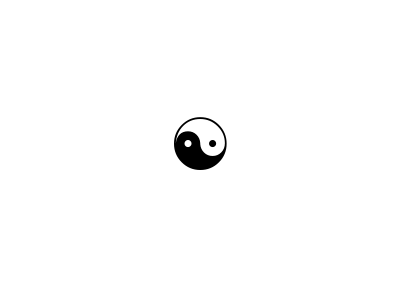

```mathematica
Graphics[Text[Style["☯",288]],Method->"ShrinkWrap"->True]
```

```mathematica
Style["☯",288]
```

☯

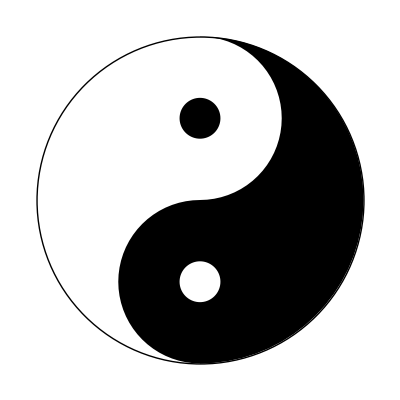

```mathematica
d[y_,r_:1/2,a_:{0,2}]:=Disk[{0,y},r,a π];
p={{0,2,{1,3}},{0,2,{3,5}},{1},{-1},{-1,1/4},{1,1/4}}/2;
Graphics@{Riffle[d@@@p,{White,Black},{1,-1,2}],Circle[]}
```

```mathematica
ClearAll[ls]
ls=Table[{5,k},{k,0,5}]
Union[Map[#[[1]]+#[[2]]I&,ls],Rest[Map[#[[1]]I+#[[2]]&,ls]]]
ls=AppendTo[ls,ls];
```

## Curves

```mathematica
ClearAll[a,b,c];
a=0.65;
b=0.85;
c=0.04;
Manipulate[PolarPlot[c √((a^2 Sin[t]^2-b^2 Cos[t]^2)/(Sin[t]^2-Cos[t]^2)),{t,0,s π},Axes->False],{{a,0.05},0,1},{{b,0.1},0,1},{{c,0.4},0,1},{{s,2},2,24}]
```

## tmp-1: Various stuff to sort out

### tmp-1

```mathematica
g[fun_]:={FunctionInjective[fun[x],x],FunctionSurjective[fun[x],x],FunctionBijective[fun[x],x]}
```

```mathematica
g[Sin]
g[Tan]
g[Exp]
g[#^3&]
```

{False,False,False}

{False,True,False}

{True,False,False}

{True,True,True}

```mathematica
f[x_,y_]:=x^2+y/;{x,y}≠{2,2}
Sum[f[j,k],{j,1,3},{k,1,3}]-f[2,2]
```

54

```mathematica
WeierstrassP[.2+.3I,{1,I}]
```

-2.96065-7.09502 ⅈ

```mathematica
f[z_,w1_,w2_]:=1/z^2+
Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1- j w2)^2,
{i,1,k},{j,1,k}
]+Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2,
{i,0,0},{j,1,k}
]+Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2,
{i,1,k},{j,0,0}
]/;{w1,w2}≠{0,0}
```

```mathematica
k=10;
f[.2+.3I,2,2I]
k=1000;
f[.2+.3I,2,2I]
```

-3.16452-5.99215 ⅈ

-3.16886-3.71288 ⅈ

```mathematica
WeierstrassP[.2+.3I,{1,I}]
f[z_,w1_,w2_]:=1/z^2+
Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1- j w2)^2,
{i,1,100},{j,1,100}
]/;{w1,w2}≠{0,0}
```

-2.96065-7.09502 ⅈ

```mathematica
f[.2+.3I,1,I]
```

-3.36632+2.11861 ⅈ

```mathematica
1/(2.2+2.3I)^2
```

-0.00438524-0.0986192 ⅈ

```mathematica
WeierstrassP[2.2+2.3I,{2,2I}]
f[z_,w1_,w2_]:=1/z^2+Sum[
Piecewise[{{1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2,{i,j}≠{0,0}},{0,True}}],
{i,-k,k},{j,-k,k}]/;{w1,w2}≠{0,0}
k=0;
f[2.2+2.3I,2,2I]
k=15;
f[2.2+2.3I,2,2I]
```

-7.53012-12.3981 ⅈ

-0.00438524-0.0986192 ⅈ

-2.98777-7.03242 ⅈ

```mathematica
g[z_,w1_,w2_,i_,j_]:=1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2
g[.2+.3I,1,I,110050,175]
```

-3.02261×10^-16-4.48734×10^-16 ⅈ

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{z,0,20}]//Normal
```

1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)+(z^10 Gamma[1/4]^24)/(2617245696000 π^6)+(z^14 Gamma[1/4]^32)/(91122026151936000 π^8)+(z^18 Gamma[1/4]^40)/(3499085804234342400000 π^10)

```mathematica
g[z_]:=1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)+(z^10 Gamma[1/4]^24)/(2617245696000 π^6)+(z^14 Gamma[1/4]^32)/(91122026151936000 π^8)+(z^18 Gamma[1/4]^40)/(3499085804234342400000 π^10)
g[z_]:=1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)
```

```mathematica
WeierstrassP[0.05+0.05I,{6,111I}]
WeierstrassP[0.05+0.05I,{6,101I}]
WeierstrassP[0.05+0.05I,{2,2I}]
g[0.05+0.05I]
```

2.44249×10^-14-199.999 ⅈ

-2.44249×10^-14-199.999 ⅈ

6.43929×10^-15-200. ⅈ

8.3268×10^-15-199.997 ⅈ

```mathematica
WeierstrassP[1+I, WeierstrassInvariants[{1, I}]]//N//Chop
```

0

```mathematica
DSolve[{y''[x]==x  y[x]}, y[x], x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
f[z_]:=Sin[z]/z
g[w_]:=(Series[f[z],{z,0,18}]//Normal)/.z:> w
h[w_]:=Sinc[w]
```

```mathematica
f[0.1]//N
g[0.1]//N
h[0.1]//N
Limit[f[z],z->0]
```

0.998334

0.998334

0.998334

1

```mathematica
Series[Sin[z]/z,{z,0,6}]
Series[Sinc[z],{z,0,6}]
```

1-z^2/6+z^4/120-z^6/5040+O[z]^7

1-z^2/6+z^4/120-z^6/5040+O[z]^7

```mathematica
(Series[ⅇ^(1/z),{z,Infinity,12}]//Normal)
```

1+1/(479001600 z^12)+1/(39916800 z^11)+1/(3628800 z^10)+1/(362880 z^9)+1/(40320 z^8)+1/(5040 z^7)+1/(720 z^6)+1/(120 z^5)+1/(24 z^4)+1/(6 z^3)+1/(2 z^2)+1/z

```mathematica
Residue[1/(z-1),{z,1}]
```

1

```mathematica
f[z_]:=ⅇ^(1/z)
f[.1+.1I]
f[.01+.1I]
f[.001+.1I]
f[.0001+.0001I]
f[.0001+.001I]
```

42.0992+142.317 ⅈ

-2.39204+1.23383 ⅈ

-0.927909+0.600303 ⅈ

4.58998352293687×10^2170+2.93191724614707×10^2171 ⅈ

-8.77757×10^42+4.76476×10^42 ⅈ

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
Integrate[Sin[x]/x,{x,-Infinity,Infinity}]
```

π/2

π

```mathematica
Log[1]
```

0

```mathematica
ⅇ^(1+(1+2π )I)//N
ⅇ^(1+(1+12π )I)//N
ⅇ^(1+(1+26π )I)//N
```

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

```mathematica
Log[1.4686939399158856+1+(1+26π )I]//N
```

4.41544+1.54095 ⅈ

```mathematica
Exp[Log[1/2+3I]-80 π I]//FullSimplify
```

1/2+3 ⅈ

```mathematica
FunctionAnalytic[Log[z],z,Complexes]
```

False

```mathematica
11.07/π
```

3.52369

```mathematica
Log[1]
```

0

```mathematica
f[t_]:=Log[4+ⅇ^(I t)]
f[0.]
f[6 π]//N
f[16 π]//N
```

1.60944+0. ⅈ

1.60944

1.60944

```mathematica
Series[1/(z-1),{z,Infinity,6}]
Series[1/(1-1/2 z),{z,0,6}]
```

1/z+(1/z)^2+(1/z)^3+(1/z)^4+(1/z)^5+(1/z)^6+O[1/z]^7

1+z/2+z^2/4+z^3/8+z^4/16+z^5/32+z^6/64+O[z]^7

```mathematica
1/(z-1)+1/(1-1/2 z)//Factor
```

-z/((-2+z) (-1+z))

```mathematica
Series[z ⅇ^(1/z),{z,Infinity,12}]
```

z+1+1/(2 z)+1/(6 z^2)+1/(24 z^3)+1/(120 z^4)+1/(720 z^5)+1/(5040 z^6)+1/(40320 z^7)+1/(362880 z^8)+1/(3628800 z^9)+1/(39916800 z^10)+1/(479001600 z^11)+1/(6227020800 z^12)+O[1/z]^13

```mathematica
Apart[1/((z-1)(z-2)),z]
```

1/(-2+z)-1/(-1+z)

```mathematica
Series[ⅇ^(1/z),{z,Infinity,12}]
```

1+1/z+1/(2 z^2)+1/(6 z^3)+1/(24 z^4)+1/(120 z^5)+1/(720 z^6)+1/(5040 z^7)+1/(40320 z^8)+1/(362880 z^9)+1/(3628800 z^10)+1/(39916800 z^11)+1/(479001600 z^12)+O[1/z]^13

```mathematica
Series[1/((z-1)(z-2)),{z,0,4}]
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+O[z]^5

```mathematica
(Series[1/(z-2),{z,0,4}]//Normal)-(Series[1/(z-1),{z,0,4}]//Normal)
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32

```mathematica
Series[1/(z-2),{z,0,4}]//Normal
```

-1/2-z/4-z^2/8-z^3/16-z^4/32

```mathematica
Series[1/(z-1),{z,Infinity,12}]//Normal
```

1/z^12+1/z^11+1/z^10+1/z^9+1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2+1/z

```mathematica
Apart[1/(z(z-1)),z]
```

1/(-1+z)-1/z

```mathematica
Series[1/(z(z-1)),{z,0,6}]
```

-1/z-1-z-z^2-z^3-z^4-z^5-z^6+O[z]^7

```mathematica
Series[1/(z(z-1)),{z,Infinity,6}]
```

(1/z)^2+(1/z)^3+(1/z)^4+(1/z)^5+(1/z)^6+O[1/z]^7

```mathematica
DSolve[{-y[t]==x'[t],x[t]==y'[t]},{y[t],x[t]},t]
```

{{x[t]→C[1] Cos[t]-C[2] Sin[t],y[t]→C[2] Cos[t]+C[1] Sin[t]}}

```mathematica
m:={{4,-1},{0,0.25}}
m.{{1+0.5I},{0.5-2I}}//mf
```

(3.5+4. ⅈ
0.125-0.5 ⅈ)

```mathematica
Orthogonalize[{{3/2,1},{-2,-1/2}}]
```

{{3/(√13),2/(√13)},{-2/(√13),3/(√13)}}

```mathematica
{3/2,1}.{-2,-1/2}
```

-7/2

```mathematica
{3/(√13),2/(√13)}.{-2/(√13),3/(√13)}
```

0

```mathematica
(3/(√13))^2+(2/(√13))^2
```

1

### tmp-2

```mathematica
rr=3;
torus[u_,v_]:={(rr+Cos[2 Pi u]) Cos[2 Pi v],(rr+Cos[2 Pi u]) Sin[2 Pi v],Sin[2 Pi u]}
tor=ParametricPlot3D[torus[u,v],{u,0,1},{v,0,1},Boxed->False,MeshStyle->None];
knt=ParametricPlot3D[torus[1,u],{u,0,1},Boxed->False,Axes->False];
grp0=Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}];
grp1=Graphics3D[{PointSize[0.02],Point[{0,4,0.5}]}];
Show[tor,knt,grp1]
```

-Graphics3D-

```mathematica
Show[knt,grp1]
```

-Graphics3D-

### tmp-3

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
p[5.35]//N//Chop
p[5.35+17(2+2I)]//N//Chop
```

2.62542

2.62542

```mathematica
123
```

123

```mathematica
Solve[WeierstrassP[1.4+0.6I,WeierstrassInvariants[{1,I}]]==WeierstrassP[x,WeierstrassInvariants[{1,I}]],x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→ConditionalExpression[(0.6+1.4 ⅈ)+2. C[1]+(0.+2. ⅈ) C[2], (C[1]|C[2])∈ℤ]},{x→ConditionalExpression[(1.4+0.6 ⅈ)+2. C[1]+(0.+2. ⅈ) C[2], (C[1]|C[2])∈ℤ]}}

```mathematica
WeierstrassP[1.4+0.6I,WeierstrassInvariants[{1,I}]]//Chop

WeierstrassP[0.6+1.4I,WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[4.6+3.4I,WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[3.4+2.6I,WeierstrassInvariants[{1,I}]]//Chop
```

((1.77636×10^-15+1.00495 ⅈ) Chop)[((-1.59872×10^-14+1.00495 ⅈ) Chop)[((-9.54792×10^-15+1.00495 ⅈ) Chop)[0.+1.00495 ⅈ]]]

```mathematica
((1.5+1.4I+3000(2+2I))+(0.5+0.6I+111(2+2I)))/(2+2I)
```

3112.+0. ⅈ

```mathematica
WeierstrassP[7.25+10.5I,WeierstrassInvariants[{1,I}]]//N
WeierstrassP[1.25+4.5I,WeierstrassInvariants[{1,I}]]//N
```

0.603561+0.717759 ⅈ

0.603561+0.717759 ⅈ

```mathematica
ClearAll[f]
f[x_]:=WeierstrassP[x,WeierstrassInvariants[{1,I}]]
u=1.2+1.2I
v=0.3+0.7I
f[u+v]-f[u-v]//N
-(f'[u]f'[v])/(f[u]-f[v])^2//N
f[.75+.85I]//N
f[1.25+1.15I]//N
```

1.2+1.2 ⅈ

0.3+0.7 ⅈ

2.99571-1.15055 ⅈ

2.99571-1.15055 ⅈ

-0.119239-0.221675 ⅈ

-0.119239-0.221675 ⅈ

```mathematica
ClearAll[f]
DSolve[f'[x]==√q[f[x]],f[x],x]
```

$Aborted

### tmp-4

```mathematica
ClearAll[f]
f[x_]:=WeierstrassP[x,WeierstrassInvariants[{4,4I}]]
g[x_]:=WeierstrassPPrime[x,WeierstrassInvariants[{4,4I}]]^3
h[x_]:=WeierstrassPPrime[x,WeierstrassInvariants[{4,4I}]]

g[2.2+1.3I]//Chop;
-g[-(2.2+1.3I)]//Chop;
g[1.8+2.7I]g[1.8+2.7I]//Chop;
g[-(1.8+2.7I)]g[-(1.8+2.7I)]//Chop;


R[z_]:=(g[z]+g[-z])/2
S[z_]:=((g[z]-g[-z])/2)/h[z]
T[z_]:=R[z]+h[z]S[z]

u=1.8+2.7I;
g[u]//Chop
T[u]//Chop
S[u]
S[-u]
T[u]
-T[-u]
```

0.000211434+0.00025694 ⅈ

0.000211434+0.00025694 ⅈ

0.00399497+0.00266427 ⅈ

0.00399497+0.00266427 ⅈ

0.000211434+0.00025694 ⅈ

0.000211434+0.00025694 ⅈ

```mathematica
ComplexPlot3D[g[z],{z,0,4+4I}]
```

-Graphics3D-

```mathematica
ComplexPlot[g[z],{z,0,8+8I},Frame->False]
```

-Graphics-

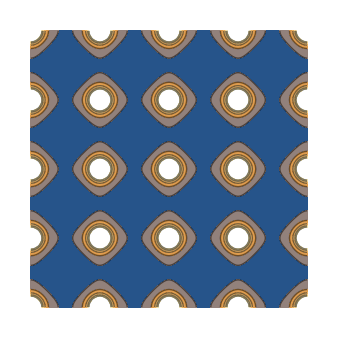

```mathematica
ComplexContourPlot[Abs[p[z]],{z,0,8+8I},Frame->False]
```

```mathematica
ColorData["Gradients"]//tf;
```

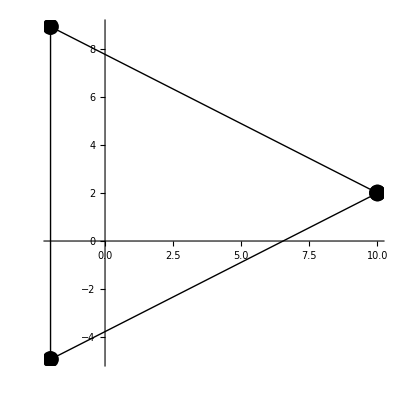

```mathematica
pad=2+2I+8cPath[3];
cPlotPath[pad,AxesOrigin->{0,0}]
```

```mathematica
1/(2π I)cContourIntegral[g'[z]/g[z],z,pad]//N
```

-5.23025×10^-15-6.40528×10^-15 ⅈ

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
q[z_]:=(p[z]-p[3+3I])/(p[z]-p[2+2I])
r[a_]:=p[a]/q[a]
```

```mathematica
r[1.2]//Abs
r[1.3]//Abs
r[1.4]//Abs
r[3.5+7.25I]//Abs
```

6.42775×10^60

6.42775×10^60

6.42775×10^60

«1 more identical outputs»

### tmp-5

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
```

```mathematica
p''[1.]
```

11.817

```mathematica
Series[Exp[-1/z],{z,Infinity,10}]
```

1-1/z+1/(2 z^2)-1/(6 z^3)+1/(24 z^4)-1/(120 z^5)+1/(720 z^6)-1/(5040 z^7)+1/(40320 z^8)-1/(362880 z^9)+1/(3628800 z^10)+O[1/z]^11

```mathematica
Accumulate[Table[(n+2)^2-n^2,{n,1,401,2}]]//Total
Accumulate[Table[4n+4,{n,1,401,2}]]//Total
```

10989608

10989608

```mathematica
Table[{k,BaseForm[k,5]},{k,1,25}]
```

{{1,1_5},{2,2_5},{3,3_5},{4,4_5},{5,10_5},{6,11_5},{7,12_5},{8,13_5},{9,14_5},{10,20_5},{11,21_5},{12,22_5},{13,23_5},{14,24_5},{15,30_5},{16,31_5},{17,32_5},{18,33_5},{19,34_5},{20,40_5},{21,41_5},{22,42_5},{23,43_5},{24,44_5},{25,100_5}}

```mathematica
ClearAll[f]
f[n_]:={n,Ceiling[(√(n+1)-1)/2],8Ceiling[(√(n+1)-1)/2],8(Ceiling[(√(n+1)-1)/2]-Floor[(√(n+1)-1)/2]),(√(n+1)-1)/2}
Table[f[k],{k,1,49}]//tf
```

1 | 1 | 8 | 8 | 1/2 (-1+√2)
2 | 1 | 8 | 8 | 1/2 (-1+√3)
3 | 1 | 8 | 8 | 1/2
4 | 1 | 8 | 8 | 1/2 (-1+√5)
5 | 1 | 8 | 8 | 1/2 (-1+√6)
6 | 1 | 8 | 8 | 1/2 (-1+√7)
7 | 1 | 8 | 8 | 1/2 (-1+2 √2)
8 | 1 | 8 | 0 | 1
9 | 2 | 16 | 8 | 1/2 (-1+√10)
10 | 2 | 16 | 8 | 1/2 (-1+√11)
11 | 2 | 16 | 8 | 1/2 (-1+2 √3)
12 | 2 | 16 | 8 | 1/2 (-1+√13)
13 | 2 | 16 | 8 | 1/2 (-1+√14)
14 | 2 | 16 | 8 | 1/2 (-1+√15)
15 | 2 | 16 | 8 | 3/2
16 | 2 | 16 | 8 | 1/2 (-1+√17)
17 | 2 | 16 | 8 | 1/2 (-1+3 √2)
18 | 2 | 16 | 8 | 1/2 (-1+√19)
19 | 2 | 16 | 8 | 1/2 (-1+2 √5)
20 | 2 | 16 | 8 | 1/2 (-1+√21)
21 | 2 | 16 | 8 | 1/2 (-1+√22)
22 | 2 | 16 | 8 | 1/2 (-1+√23)
23 | 2 | 16 | 8 | 1/2 (-1+2 √6)
24 | 2 | 16 | 0 | 2
25 | 3 | 24 | 8 | 1/2 (-1+√26)
26 | 3 | 24 | 8 | 1/2 (-1+3 √3)
27 | 3 | 24 | 8 | 1/2 (-1+2 √7)
28 | 3 | 24 | 8 | 1/2 (-1+√29)
29 | 3 | 24 | 8 | 1/2 (-1+√30)
30 | 3 | 24 | 8 | 1/2 (-1+√31)
31 | 3 | 24 | 8 | 1/2 (-1+4 √2)
32 | 3 | 24 | 8 | 1/2 (-1+√33)
33 | 3 | 24 | 8 | 1/2 (-1+√34)
34 | 3 | 24 | 8 | 1/2 (-1+√35)
35 | 3 | 24 | 8 | 5/2
36 | 3 | 24 | 8 | 1/2 (-1+√37)
37 | 3 | 24 | 8 | 1/2 (-1+√38)
38 | 3 | 24 | 8 | 1/2 (-1+√39)
39 | 3 | 24 | 8 | 1/2 (-1+2 √10)
40 | 3 | 24 | 8 | 1/2 (-1+√41)
41 | 3 | 24 | 8 | 1/2 (-1+√42)
42 | 3 | 24 | 8 | 1/2 (-1+√43)
43 | 3 | 24 | 8 | 1/2 (-1+2 √11)
44 | 3 | 24 | 8 | 1/2 (-1+3 √5)
45 | 3 | 24 | 8 | 1/2 (-1+√46)
46 | 3 | 24 | 8 | 1/2 (-1+√47)
47 | 3 | 24 | 8 | 1/2 (-1+4 √3)
48 | 3 | 24 | 0 | 3
49 | 4 | 32 | 8 | 1/2 (-1+5 √2)

```mathematica
Sum[(MoebiusMu[n] x^n)/(1-x^n),{n,1,Infinity}]
```

x

```mathematica
10^22/2.
```

5.×10^21

```mathematica
IntegerPartitions[19]//Length
```

490

## tmp-2: makeEllipticFunction ( TBD: WeierstrassSigma -> EllipticTheta )

```mathematica
ClearAll[makeEllipticFunction]
makeEllipticFunction[z_,{ω1_,ω3_},zeros_?VectorQ,poles_?VectorQ]:=Module[
{c=π/(2 ω1),q=Exp[I π ω3/ω1]},
(Product[EllipticTheta[1,c (z-r),q],{r,zeros}]/Product[EllipticTheta[1,c (z-s),q],{s,poles}])(EllipticTheta[1,c (z-Last[poles]),q]/EllipticTheta[1,c (z-Last[poles]-(Total[zeros]-Total[poles])),q])]/;Length[zeros]==Length[poles]&&With[{wl={ω1,ω3,Total[zeros]-Total[poles]}},PossibleZeroQ[wl.FindIntegerNullVector[wl]]]
```

```mathematica
makeEllipticFunction[z_, {ω1_, ω3_}, zeros_List,poles_List]:=Module[{g2,g3,σ},
{g2,g3}=WeierstrassInvariants[N[{ω1,ω3}]];σ=WeierstrassSigma[#,{g2,g3}]&;(Times @@σ[z-zeros])/(Times @@σ[z-poles])σ[z-Last[poles]]/σ[z-Last[poles]-(Total[zeros]-Total[poles])]]/;Length[zeros]==Length[poles]&&Resolve[Exists[{μ,ν},Element[{μ,ν},Integers],Total[zeros]-Total[poles]==μ ω1+ν ω3]]
```

```mathematica
f[z_]=makeEllipticFunction[z,{1,I},{1/4+1/4 I,1/4+1/4 I,-1/2-1/2 I},{0,0,0}] // Chop;

f[z_]=makeEllipticFunction[z,{1,I},{
1/4+1/4 I,
1/4+1/4 I,
-1/2-1/2 I,
1/10+2/10I,
1/10+2/10I,
-2/10-4/10I
},{0,0,0,0,0,0}] // Chop
```

(EllipticTheta[1,1/2 π ((-1/4-ⅈ/4)+z),ⅇ^-π]^2 EllipticTheta[1,1/2 π ((-1/10-ⅈ/5)+z),ⅇ^-π]^2 EllipticTheta[1,1/2 π ((1/5+(2 ⅈ)/5)+z),ⅇ^-π] EllipticTheta[1,1/2 π ((1/2+ⅈ/2)+z),ⅇ^-π])/(EllipticTheta[1,(π z)/2,ⅇ^-π]^6)

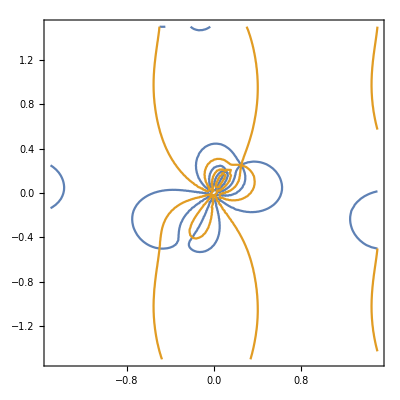

```mathematica
ContourPlot[Evaluate[{Re[f[x+I y]]==0,Im[f[x+I y]]==0}],{x,-1.5,1.5},{y,-1.5,1.5}]
```

```mathematica
ComplexPlot[f[z],{z,-(2+2I),(2+2I)}]
```

-Graphics-

```mathematica
ComplexPlot3D[f[z],{z,-(2+2I),(2+2I)}]
```

-Graphics3D-

## UZT-1: Are both Sums equal ?

```mathematica
Sum[1/(n+τ)^k,{n,-Infinity,Infinity},Assumptions->{k≥2}]//FullSimplify
```

(-1)^-k HurwitzZeta[k,1-τ]+HurwitzZeta[k,τ]

```mathematica
(-2 π ⅈ)^k/((k-1)!)Sum[m^(k-1)ⅇ^(2 π ⅈ τ m),{m,1,Infinity}]
```

((-2 ⅈ π)^k PolyLog[1-k,ⅇ^(2 ⅈ π τ)])/((-1+k)!)

## UZT-2:

```mathematica
ClearAll[q,f1,f2,k]
q[z_]:=Exp[2 π ⅈ z]
f1[z_,k_]:=Sum[n^(2k-1)q[z]^n/(1-q[z]^n),{n,1,Infinity}]
f2[z_,k_]:=Sum[DivisorSigma[k,n]q[z],{n,1,Infinity}]
f1[0.5I,4]//N
f2[0.5I,4]//N
```

0.532143

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

800.601

```mathematica
ClearAll[f1,f2,n,k,x]
f1[k_,x_]:=Sum[n^k x^n/(1-x^n),{n,1,Infinity}]
f2[k_,x_]:=Sum[DivisorSigma[k,n] x^n,{n,1,Infinity}]
```

```mathematica
f1[3,0.6]//N
f2[3,0.6]//N
f1[7,0.16]//N
f2[7,0.16]//N
```

95.3671

95.3671

39.7804

39.7804

## UZT-3: Bouw nSumPrime

```mathematica
SetAttributes[nSumPrime,HoldAll]
(*nSumPrime[f_[a___,var_,b___],{var_,xmin_,xmax_}]:=ListPlot[Table[{y,f[a,y,b]},{y,xmin,xmax,(xmax-xmin)/100}]]*)
nSumPrime[f_[var_]]:=Sum[f[var]+f[-var],{var,1,Infinity}]

g1[m_]:=(1/(z+m)-1/m)
1/z+nSumPrime[g1[n]]//FullSimplify
```

π Cot[π z]

```mathematica
g2[m_]:=m^-2
nSumPrime[g2[n]]//FullSimplify
```

π^2/3

```mathematica
Interpreter["Date"]["17/2-'59"]
```

Failure[…]

```mathematica
DateObject[DateFormat->{"DayShort","/","MonthShort","-'","YearShort"}]
```

6/6-'21GMT+2

## Test

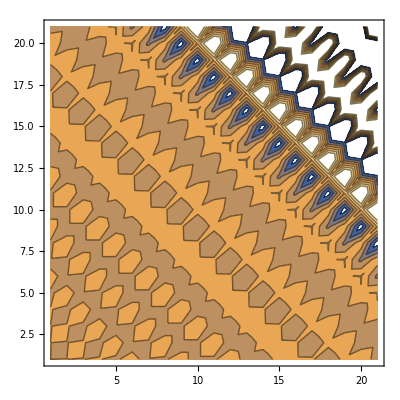

```mathematica
ListContourPlot[Table[RamanujanTau[x+ y],{x,0,20,1},{y,0,20,1}]]
```

```mathematica
Series[Product[1-q^n,{n,1,Infinity}],{q,0,11}]
```

1-q-q^2+q^5+q^7+O[q]^12

# Revision Apostol MFDSNT

1. Elliptic Functions

## makeEllipticFunction

```mathematica
w1=1;
w2=I;
f[z_]=ResourceFunction["MakeEllipticFunction"][z,{2w1,2 w2},{1/2,(1+I)/2},{0,I/2}];
```

```mathematica
GraphicsRow[{ComplexPlot3D[f[z],{z,-(2w1+2w2),(2w1+2w2)}],ComplexPlot[f[z],{z,-2(2w1+2w2),2(2w1+2w2)}]}]
```

-Graphics-

## temp-1